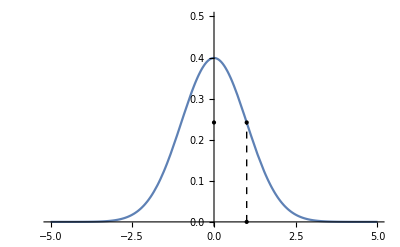

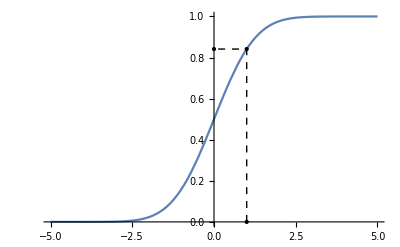

1/2 (1+Erf[1/(√2)])

0.841345

```mathematica
nd=NormalDistribution[];

Plot[PDF[nd,x],{x,-5,5},PlotRange->{0,0.5},
Epilog-> {Point[{1,0}],Point[{1,PDF[nd,1]}],Point[{0,PDF[nd,1]}],
Dashed,
Line[{{1,0},{1,PDF[nd,1]}}]}]

Plot[CDF[nd,x],{x,-5,5},
Epilog-> {Point[{1,0}],Point[{1,CDF[nd,1]}],Point[{0,CDF[nd,1]}],
Dashed,
Line[{{1,0},{1,CDF[nd,1]},{0,CDF[nd,1]}}]}]

Probability[x≤1,x\[Distributed]NormalDistribution[]]
%//N
```

```mathematica
Probability[x≤1,x\[Distributed]NormalDistribution[m,s]]
```

1/2 (1-Erf[3333/(1000 √2)])

```mathematica
Probability[0≤x≤1,x\[Distributed]NormalDistribution[m,s]]
```

1/2 (-Erf[3333/(1000 √2)]+Erf[(5 √2)/3])

```mathematica
Probability[x≤-1||x≥1 ,x\[Distributed]NormalDistribution[m,s]]
Probability[x≤-1∨x≥1 ,x\[Distributed]NormalDistribution[m,s]]
```

1/2 (2-Erfc[3333/(1000 √2)]+Erfc[10001/(3000 √2)])

1/2 (2-Erfc[3333/(1000 √2)]+Erfc[10001/(3000 √2)])

```mathematica
Probability[x≤-1&&x≥1 ,x\[Distributed]NormalDistribution[m,s]]
Probability[x≤-1∧x≥1 ,x\[Distributed]NormalDistribution[m,s]]
```

0

0

```mathematica
Probability[x≤ 2,x\[Distributed]{1,2,3,4,5,6}]
```

1/3

```mathematica
Probability[x^2>4∨Abs[x]<1,x\[Distributed]{1,2,3,4,5,6}]
```

2/3

Условная вероятность (вероятность при условии)

```mathematica
Probability[x≤0\[Conditioned]x≤0 ,x\[Distributed]NormalDistribution[0,1]]
```

1

Математическое ожидание

```mathematica
Mean[NormalDistribution[]]
Expectation[x,x\[Distributed]NormalDistribution[]]
Expectation[2x+3,x\[Distributed]NormalDistribution[]]
Expectation[x\[Conditioned]-1<x≤1,x\[Distributed]NormalDistribution[0,1]]
Expectation[x\[Conditioned]x≤0,x\[Distributed]NormalDistribution[0,1]]
```

0

0

3

0

-√(2/π)

#### Поиск параметров распределений

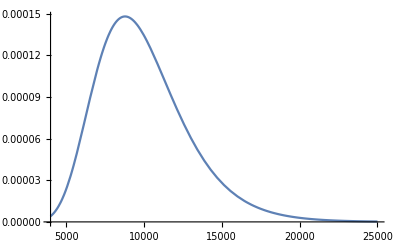

```mathematica
m=10000;
s=3000;
dist=LogNormalDistribution[μ,σ];
sol=Solve[
{
Mean[dist]==m,
StandardDeviation[dist]==s
},
{μ,σ},Reals
];
{mlog,slog}={μ,σ}/.Last[ sol];
Plot[
PDF[LogNormalDistribution[mlog,slog],x],{x,4000,25000}
]
```

#### Страхование

Страховой полис возмещает потери до  10 ден. ед. 
Убытки держателя страхового полиса подчиняются следующему распределению с функцией плотности 2 / y ^ 3  для  y> 1 и 0 в противном случае. 
Найдите ожидаемую размер выплат  по страховому полису.

```mathematica
dist=CensoredDistribution[{1,10},ProbabilityDistribution[2/y^3,{y,1,Infinity}]];
Expectation[x, x\[Distributed]dist]
%//N
```

19/10

1.9

ProbabilityDistribution[2/x^3,{x,1,∞}]

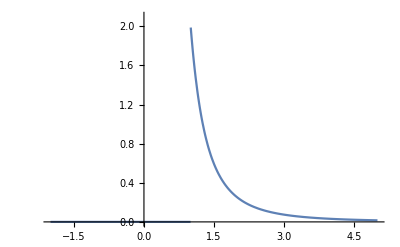

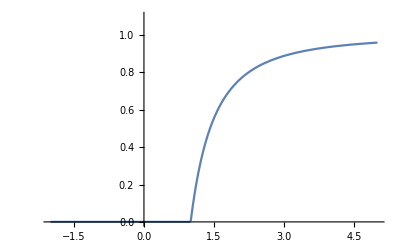

```mathematica
pd=ProbabilityDistribution[2/y^3,{y,1,Infinity}]
Plot[PDF[pd,x],{x,-2,5},PlotRange->{0,2.1}]
Plot[CDF[pd,x],{x,-2,5},PlotRange->{0,1.1}]
```

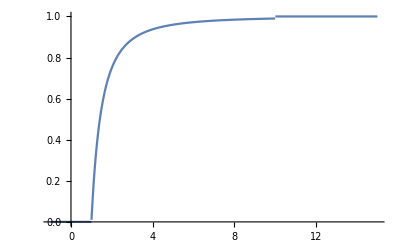

```mathematica
Plot[
CDF[
CensoredDistribution[
{1,10},
ProbabilityDistribution[2/x^3,{x,1,Infinity}]],x]//Evaluate,{x,-1,15}]
```

```mathematica
Plot[
CDF[
CensoredDistribution[
{1,10},
ProbabilityDistribution[2/x^3,{x,1,Infinity}]],x]//Evaluate,{x,-1,15}]
```

-Graphics-

Ежемесячные выплаты страховой компании моделируются непрерывной положительной случайной переменной x, функция плотности вероятности которой пропорциональна 1 / (x + 1) ^ 4, где 0 <x <∞. Определите ожидаемые ежемесячные выплаты компании:

```mathematica
claimDistribution=ProbabilityDistribution[3/(1+x)^4,{x,0,Infinity}];
Expectation[x,x\[Distributed]claimDistribution]
```

1/2

Сумма выплат по повреждениям домов от ветра представляет собой независимые случайные величины с общей функцией плотности 3/x^4 для x> 1 и 0, в противном случае, где x - сумма требования в тысячах. Предположим, что три подобные  выплаты будут произведены. Найдите ожидаемое значение самой большой из трех выплат:

```mathematica
windClaims=ProductDistribution[{ProbabilityDistribution[3/y^4,{y,1,Infinity}],3}];
Expectation[1000Max[x,y,z],{x,y,z}\[Distributed]windClaims]
```

2025

Пусть x возраст автомобиля участвующего в аварии. Пусть y отношение промежутка времени до страхового случая к промежутку действия страховки. x и y имеют совместную функцию плотности вероятности (10-x y ^ 2) / 64 для 2 <= x <= 10 и 0 <= y <= 1, а 0 в противном случае. 
Рассчитайте ожидаемый возраст застрахованного автомобиля, участвующего в аварии:

```mathematica
ageDistribution=ProbabilityDistribution[(10-x y^2)/64,{x,2,10},{y,0,1}];
Expectation[x,{x,y}\[Distributed]ageDistribution]
N[%,3]
```

52/9

5.78

Уровнем удержания называется сумма зафиксированная в договоре между страховщиком и перестраховщиком при превышении которой убытки делятся между ними. До этой суммы убытки покрываются страховщиком.
Вычислить ожидаемое значение сумм y и z, выплачиваемых страховщиком и перестраховщиком, для уровня удержания m, если претензии следуют за логнормальным распределением с параметрами μ и σ. Найдите ожидаемые выплаты страховщиком:

```mathematica
insurerPayouts=TransformedDistribution[Min[x,m],x\[Distributed]LogNormalDistribution[μ,σ], Assumptions->m>0];
Expectation[y, y\[Distributed]insurerPayouts]
```

1/2 (10000+10000 Erf[(μ-Log[10000])/(√2 σ)]+ⅇ^(μ+σ^2/2) Erfc[(μ+σ^2-Log[10000])/(√2 σ)])

Найдите ожидаемые выплаты перестраховщиком страховщику:

```mathematica
reinsurerPayouts=TransformedDistribution[Max[0,x-m],x\[Distributed]LogNormalDistribution[μ,σ], Assumptions->m>0];
Expectation[z, z\[Distributed]reinsurerPayouts]
```

1/2 (-10000+ⅇ^(μ+σ^2/2)-10000 Erf[(μ-Log[10000])/(√2 σ)]+ⅇ^(μ+σ^2/2) Erf[(μ+σ^2-Log[10000])/(√2 σ)])

#### Зависимые случайные переменные

```mathematica
TransformedDistribution[u+v,{u\[Distributed]PoissonDistribution[Subscript[μ, 1]],v\[Distributed]PoissonDistribution[Subscript[μ, 2]]}]
```

PoissonDistribution[μ_1+μ_2]

```mathematica
TransformedDistribution[2 u+b,u\[Distributed]NormalDistribution[μ,σ]]
```

NormalDistribution[b+2 μ,2 σ]

```mathematica
TransformedDistribution[Exp[u],u\[Distributed]NormalDistribution[μ,σ]]
```

LogNormalDistribution[μ,σ]

Две точки выбираются случайным образом и независимо от интервала (0,1), согласно равномерному распределению. Вычислить ожидаемое расстояние между двумя точками:

```mathematica
Mean[
TransformedDistribution[
Abs[x-y],
{x,y}\[Distributed]UniformDistribution[{{0,1},{0,1}}]
]
]
```

1/3

```mathematica
pointA:=RandomVariate[UniformDistribution[{0,1}]]
pointB:=RandomVariate[UniformDistribution[{0,1}]]
Mean[Table[ Abs[pointA-pointB],{i,1,100000}]]
```

0.332355

```mathematica
Clear[α,β,n,p]
ParameterMixtureDistribution[BinomialDistribution[n,p], p \[Distributed] BetaDistribution[α,β]]
```

BetaBinomialDistribution[α,β,n]

```mathematica
ParameterMixtureDistribution[PoissonDistribution[v], v \[Distributed] ExponentialDistribution[λ]]
```

GeometricDistribution[λ/(1+λ)]

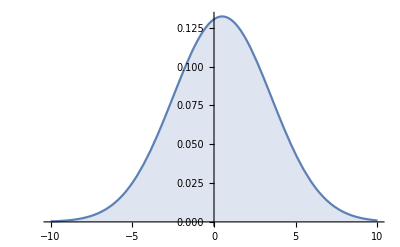

1/2 (Erf[(1-x)/(3 √2)]+Erf[x/(3 √2)])

```mathematica
Clear[m,s]
pd=ParameterMixtureDistribution[
NormalDistribution[m,3],
 m \[Distributed] UniformDistribution[{0,1}]];
Plot[Evaluate[PDF[pd,x]],{x,-10,10},Filling->Axis,PlotRange->All]
PDF[pd,x]
```

```mathematica
𝒟1=ParameterMixtureDistribution[
NormalDistribution[μ,σ],
μ\[Distributed]TransformedDistribution[x,x\[Distributed]NormalDistribution[μ1,σ]
]
]
PDF[𝒟1,x]//Evaluate
```